```mathematica
#More plots in 2D
```

2 D in plots #More

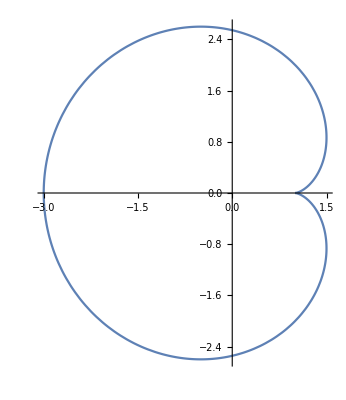

```mathematica
ParametricPlot[{2 Cos[t]-Cos[2t], 2 Sin[t] - Sin[2t]}, {t, 0, 2π}]
```



```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2π}]
```

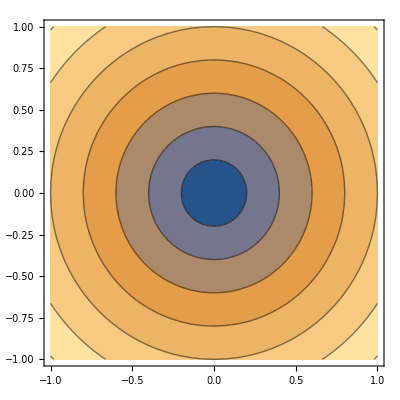

```mathematica
ContourPlot[ Sqrt[x^2+y^2], {x, -1, 1}, {y, -1, 1}]
```

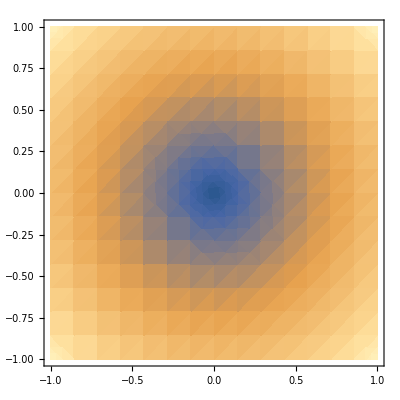

```mathematica
DensityPlot[ Sqrt[x^2+y^2], {x, -1, 1}, {y, -1, 1}]
```

```mathematica
Plot3D[x^2-y^2, {x,-3,3}, {y,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u], Cos[u], u/10}, {u, 0 ,20}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u], Cos[u], u/1}, {u, 0 ,20}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Sin[θ], {θ, 0, π}, {ϕ, 0, 2π}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[x^4-x^2, {x,-1,1}]
```

-Graphics3D-

```mathematica
D[x^3 z + 2 y^2 x + y z^3,y,z]
```

3 z^2

```mathematica
D[(x^2-2x y + x y z), x,y]
```

-2+z

```mathematica
∫∫(x^2+y^2)ⅆxⅆy
```

(x^3 y)/3+(x y^3)/3

```mathematica
Plot3D[(x^3 y)/3+(x y^3)/3,{x,-1.010986122886681,1.010986122886681},{y,-1.010986122886681,1.010986122886681}]
```

-Graphics3D-

```mathematica
∫∫∫(x^2+y^2+z^2)ⅆxⅆy ⅆ z
```

1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3

```mathematica
Simplify[1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3]
```

1/3 x y z (x^2+y^2+z^2)

```mathematica
∫_-1^1 ∫_-2^x (x Sin[y^2] + y Cos[x^2])ⅆy ⅆ x
```

1/4 (2 Cos[1]+√(2 π) (-9 FresnelC[√(2/π)]+FresnelS[√(2/π)])+2 Sin[1])

```mathematica
N[1/4 (2 Cos[1]+√(2 π) (-9 FresnelC[√(2/π)]+FresnelS[√(2/π)])+2 Sin[1])]
```

-3.22434

```mathematica
{1,2,3}.{a,b,c}
```

a+2 b+3 c

```mathematica
{1,2,3}×{a,b,c}
```

{-3 b+2 c,3 a-c,-2 a+b}

```mathematica
Norm[{1,2,3}]
```

√14

```mathematica
Projection[{8,10,20}, {1,0,0}]
```

{8,0,0}

```mathematica
VectorAngle[{1,0},{0,1}]
```

π/2

```mathematica
∇_{x,y} {x^2+y, x+y^2}
```

{{2 x,1},{1,2 y}}

```mathematica
Div[{f[x,y,z], g[x,y,z], h[x,y,z], {x,y,z}]
```

```mathematica
Div[{f[x,y,z], g[x,y,z], h[x,y,z]}, {x,y,z}]
```

h^(0,0,1)[x,y,z]+g^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]

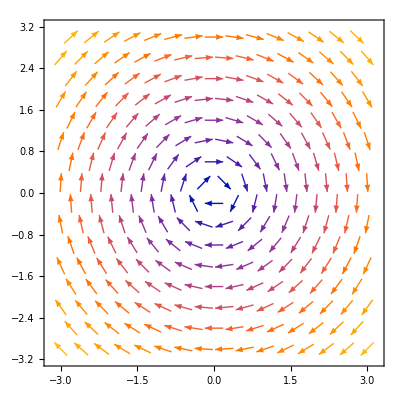

```mathematica
VectorPlot[{y,-x},{x,-3,3}, {y,-3,3}]
```

```mathematica
VectorPlot3D[{y,-x,z}, {x,-3,3}, {y,-3,3}, {z,-3,3}]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[{y,-x,z},"CenterPlanes",{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-